```mathematica
thresholdNetwork=NetChain[{LinearLayer[10, "Input"-> 10],ElementwiseLayer[If[#>0,1,0]&] }];
initializedThresholdNetwork=NetInitialize[thresholdNetwork, Method->{"Random","Biases"->NormalDistribution[],"Weights"->NormalDistribution[]},RandomSeeding->Automatic];
weights=Flatten[Normal[NetExtract[initializedThresholdNetwork,{1,"Weights"}]]];
```

Spearman Correlation: 0.209011

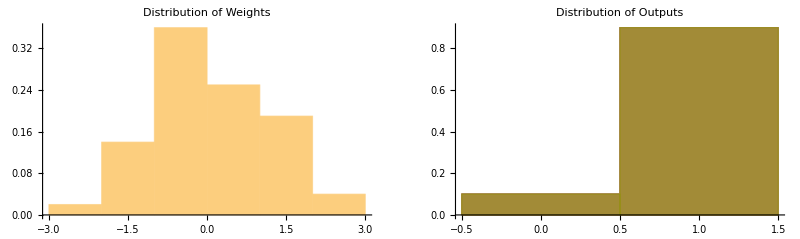

```mathematica
numSamples=10;
sampleInputs=ConstantArray[ConstantArray[0,10],numSamples];
outputs=initializedThresholdNetwork/@sampleInputs;
spearmanCorr=SpearmanRho[Flatten[Normal[weights]],Flatten[outputs]];
binnedWeights=BinLists[weights,10];
binnedOutputs=BinLists[Flatten[outputs],10];
Print["Spearman Correlation: ",spearmanCorr];
weightsHistogram=Histogram[weights,Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Weights"];
outputsHistogram=Histogram[outputs,Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Outputs"];
GraphicsGrid[{{weightsHistogram,outputsHistogram}}]
```

```mathematica
flattenedOutputs = Flatten[outputs]
(*Bin weights and outputs*)binnedWeights=BinCounts[weights,{numBins}];
binnedOutputs=BinCounts[flattenedOutputs,{numBins}];

(*Joint binning for weights and outputs*)
jointBinned=BinCounts[Transpose[{weights,flattenedOutputs}],{numBins,numBins}];

(*Convert binned counts to probabilities*)
weightsProbDist=binnedWeights/Total[binnedWeights];
outputsProbDist=binnedOutputs/Total[binnedOutputs];
jointProbDist=jointBinned/Total[jointBinned];

(*Compute entropies*)
entropyWeights=-Total[weightsProbDist Log[weightsProbDist+10^-10]];
entropyOutputs=-Total[outputsProbDist Log[outputsProbDist+10^-10]];
entropyJoint=-Total[Flatten[jointProbDist] Log[Flatten[jointProbDist]+10^-10]];

(*Calculate mutual information*)
mutualInformation=entropyWeights+entropyOutputs-entropyJoint;

(*Output the result*)
mutualInformation
```

## Testing with constant biases

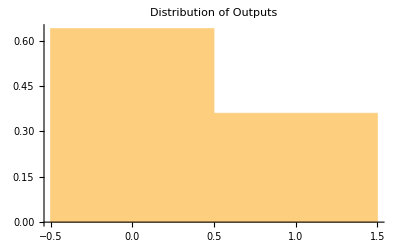

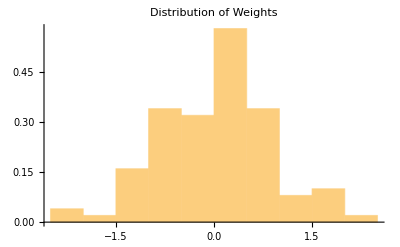

```mathematica
constantBias=0;
thresholdNetwork=NetChain[{LinearLayer[10,"Input"->10],ElementwiseLayer[If[#>0,1,0]&]}];
initializedThresholdNetwork=NetInitialize[thresholdNetwork,Method->{"Random","Biases"->NormalDistribution[],"Weights"->NormalDistribution[]},RandomSeeding->Automatic];
linearLayer=NetExtract[initializedThresholdNetwork,1];
linearLayerWithConstantBias=NetReplacePart[linearLayer,"Biases"->ConstantArray[constantBias,10]];
initializedThresholdNetworkWithConstantBias=NetReplacePart[initializedThresholdNetwork,1->linearLayerWithConstantBias];
numSamples=10;
sampleInputs=RandomVariate[NormalDistribution[],{numSamples,10}];
outputs=initializedThresholdNetworkWithConstantBias/@sampleInputs;
Histogram[Flatten[outputs],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Outputs"]
Histogram[Flatten[weights],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Weights"]
```

## Testing with Normal Distributions of Inputs, Weights, and Biases

```mathematica
thresholdNetwork=NetChain[{LinearLayer[10, "Input"-> 10],ElementwiseLayer[If[#>0,1,0]&] }];
initializedThresholdNetwork=NetInitialize[thresholdNetwork, Method->{"Random","Biases"->NormalDistribution[],"Weights"->NormalDistribution[]},RandomSeeding->Automatic];
weights=Flatten[Normal[NetExtract[initializedThresholdNetwork,{1,"Weights"}]]];
biases=Flatten[Normal[NetExtract[initializedThresholdNetwork,{1,"Biases"}]]];
```

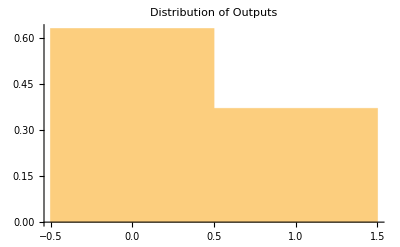

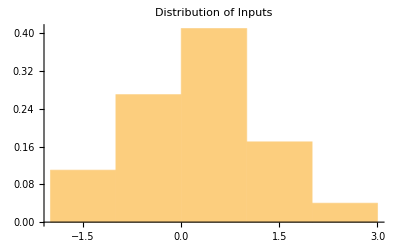

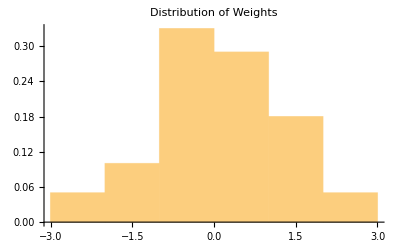

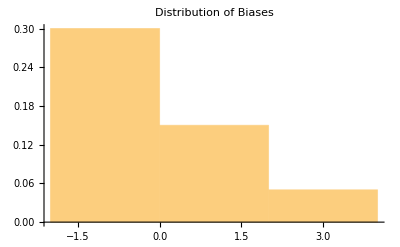

```mathematica
numSamples=10;
sampleInputs=RandomVariate[NormalDistribution[],{numSamples,10}];
outputs=initializedThresholdNetworkWithConstantBias/@sampleInputs;
Histogram[Flatten[outputs],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Outputs"]
Histogram[Flatten[sampleInputs],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Inputs"]
Histogram[Flatten[weights],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Weights"]
Histogram[Flatten[biases],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Biases"]
```

## Activation Function

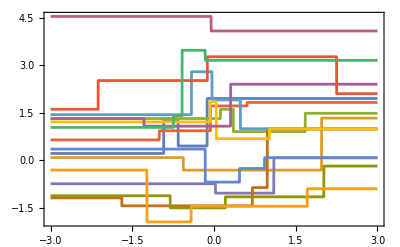
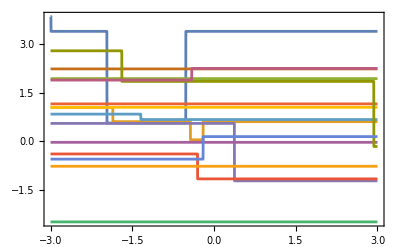
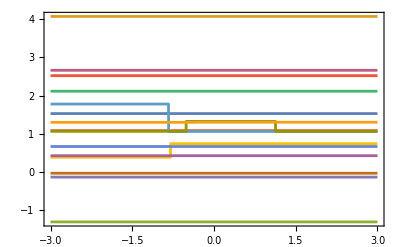
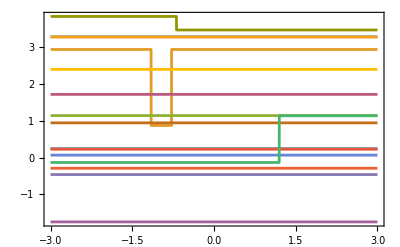
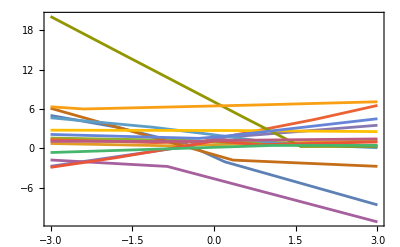
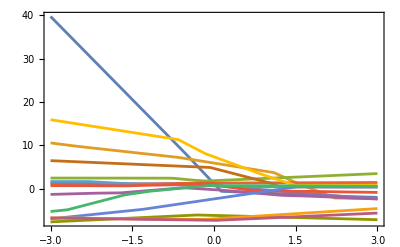
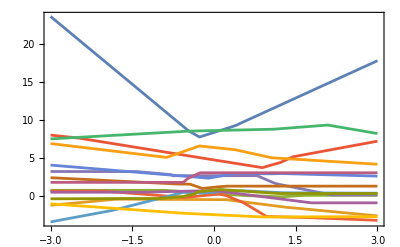
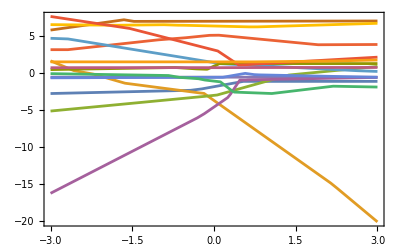
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[4]},
SeedRandom[1234];
Grid[
Append[Prepend[netPlots,""]]@Table[
Prepend[Text[act /. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},
Plot[Evaluate@Flatten@Table[
Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},
f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]
],
15
],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None
]
],{depth,{1,2,3,4}}
],{act,{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid}}
]
]
]
```

## Explanation

The above portion of code plots output functions in a grid for different activation functions and neural network depths. Each graph corresponds to the activation function on the left and the network structure directly below it, and each line within the graph corresponds to a separate initialization of weights and biases from a normal distribution with μ = 0 and σ = 1 (biases have been limited to positive values only because ............). It’s important to note that the neural structures above all consist of only one intermediate layer (this is because I found these to be the easiest to work with for this initial step given that they allow the examination of one activation function at a time). Already, we can see that some graphs (namely the ones for Sin and Tanh at later depths) become quite complicated or “messy” while others (Sigmoid and Ramp) remain relatively “clean.” This notion is the starting point for this research as the most basic generation of weights and biases along with the most basic neural network structure gives us a reference point for all other plots with manipulated parameters and their complexity.

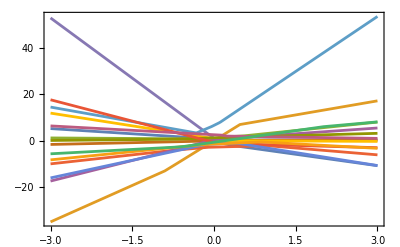
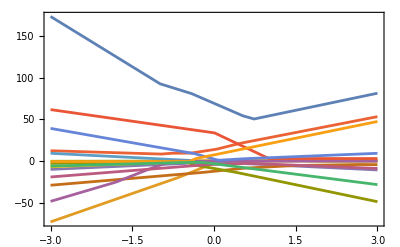
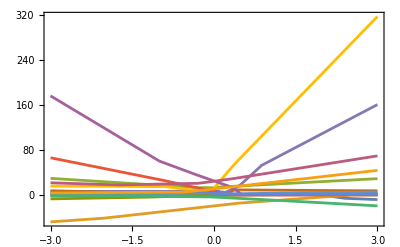
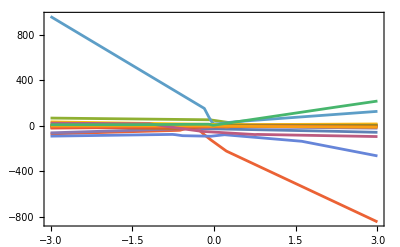
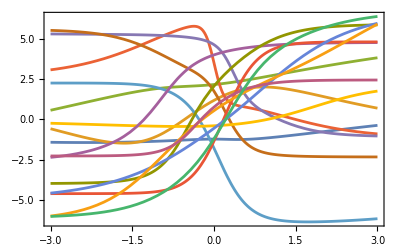
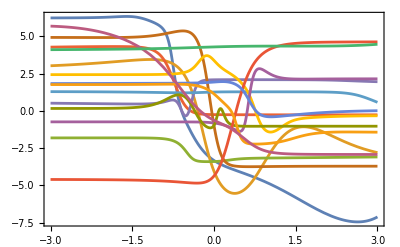
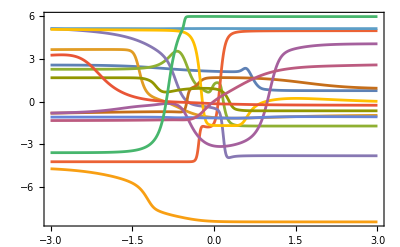
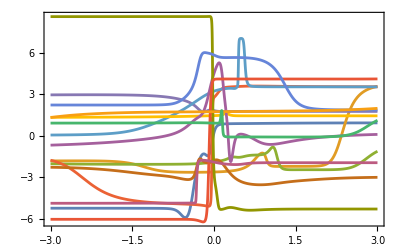
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[4]},
SeedRandom[1234];
Grid[
Append[Prepend[netPlots,""]]@Table[
Prepend[Text[act]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},
Plot[Evaluate@Flatten@Table[
Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0, 2],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0, 1]]},RandomSeeding->Automatic],f},
f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]
],
15
],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None
]
],{depth,{1,2,3,4}}
],{act,{Ramp,Tanh,Sin,LogisticSigmoid}}
]
]
]
```

## Measuring the “Smoothness” of each graph

```mathematica
fourierSmoothness[data_List]:=Module[{fTransform=Abs[Fourier[data]]},Total[(Range[0,Length[data]-1]^2)*fTransform^2]]
```

```mathematica
ChebyshevT[13,x]
```

13 x-364 x^3+2912 x^5-9984 x^7+16640 x^9-13312 x^11+4096 x^13

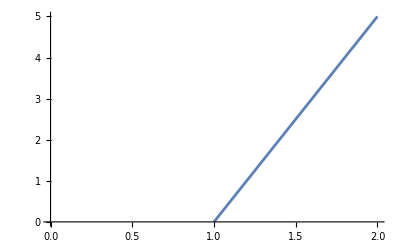

```mathematica
13 x-364 x^3+2912 x^5-9984 x^7+16640 x^9-13312 x^11+4096 x^13
```

# Objective

## Fast train

Weights

Biases

Training: learning rate

## Result or Objective Get better accuracy with less computational resources

RuleDelayed::rhs: Pattern x_ appears on the right-hand side of rule evaluateNet[net_,x_]:>Module[{f},f[x_?NumericQ]:=net[x];SetAttributes[f,Listable];f[x]].

## Manipulate for Activation Function Grid

```mathematica
With[{netPlots={{"[◼]", "NetGraphPlot"}}},Manipulate[Module[{netInit,plots,actFunc},actFunc=Switch[activationFunction,"Ramp",Ramp,"Tanh",Tanh,"Sin",Sin,"LogisticSigmoid",LogisticSigmoid];
netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[actFunc]},depth],{}],"Input"->"Real"];
plots=netPlots[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[depth];
SeedRandom[1234];
Grid[Append[Prepend[plots,""]]@Table[Prepend[Text[activationFunction]]@Table[Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None],{d,{depth}}],{activationFunction,{activationFunction}}]]],{{activationFunction,"Ramp"},{"Ramp","Tanh","Sin","LogisticSigmoid"}},{{depth,1,"Depth"},1,4,1}]]
```